Define the Hill-equation as H[x,n,k,v]:

```mathematica
H[x_,n_,k_,v_]:=(x^n)/(v*(x^n)+k^n)
```

Define the FI corresponding to a Poisson neuron with mean firing rate of H[x,n,k,v]:

```mathematica
FI[x_,n_,k_,v_]:=(D[H[x,n,k,v],x]^2)/H[x,n,k,v]
FI[x,n,k,v]
```

x^-n (k^n+v x^n) (-(n v x^(-1+2 n))/((k^n+v x^n)^2)+(n x^(-1+n))/(k^n+v x^n))^2

Calculate the integral of the FI over the range [0,1]:

```mathematica
TotalFI[n_,k_,v_]:=Integrate[FI[x,n,k,v],{x,0,1}]
TotalFI[n,k,v]
```

ConditionalExpression[1/2 k^-n ((k^n (k^n+2 k^n n+v+n v))/((k^n+v)^2)+((1+n) Hypergeometric2F1[1,(-1+n)/n,2-1/n,-k^-n v])/(-1+n)),(Re[(-k^n/v)^(1/n)]≥1||Re[(-k^n/v)^(1/n)]≤0||(-k^n/v)^(1/n)∉ℝ)&&Re[n]>1]

Re-define the integral explicitly using the previous result to speed-up computations:

```mathematica
TotalFI[n_,k_,v_]:=1/2 k^-n ((k^n (k^n+2 k^n n+v+n v))/((k^n+v)^2)+((1+n) Hypergeometric2F1[1,(-1+n)/n,2-1/n,-k^-n v])/(-1+n))
```

Plot the Total FI as a function of the Hill-coefficient n:

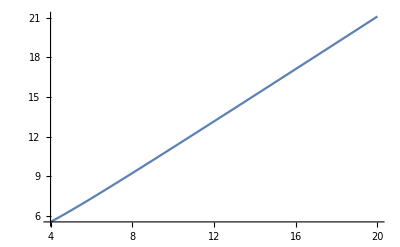

```mathematica
Plot[TotalFI[n,0.5,1],{n,4,20}]
```

Plot the Total FI as a function of the inhibitory strength v:

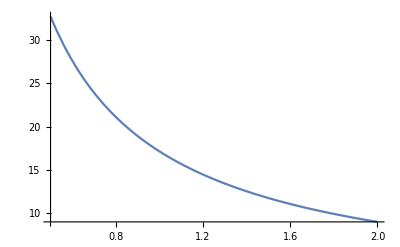

```mathematica
Plot[TotalFI[16,0.5,v],{v,0.5,2}]
```

-------------------------------------------------------------------------------------------------------------------------
In Noel et. al 2021 the authors calculate the bootstrapped total FI distribution for each of the experimental blocks from the combined subject data. Calculating 95% HDI of the total FI  results in the following ranges:

Without feedback block:

```mathematica
FindRoot[{TotalFI[AsdLowN,0.5,1]==11.8491,TotalFI[AsdHighN,0.5,1]==13.1342},{{AsdLowN,10},{AsdHighN, 10}}]
FindRoot[{TotalFI[NTLowN,0.5,1]==15.5372,TotalFI[NTHighN,0.5,1]==16.8770},{{NTLowN,10},{NTHighN, 10}}]
```

{AsdLowN→10.6789,AsdHighN→11.9843}

{NTLowN→14.4145,NTHighN→15.7655}

With feedback block 1:

```mathematica
FindRoot[{TotalFI[AsdLowN,0.5,1]==11.9354,TotalFI[AsdHighN,0.5,1]==13.3634},{{AsdLowN,10},{AsdHighN, 10}}]
FindRoot[{TotalFI[NTLowN,0.5,1]==15.8072,TotalFI[NTHighN,0.5,1]==17.2427},{{NTLowN,10},{NTHighN, 10}}]
```

{AsdLowN→10.7668,AsdHighN→12.2166}

{NTLowN→14.6869,NTHighN→77.1474}

With feedback block 2:

```mathematica
FindRoot[{TotalFI[AsdLowN,0.5,1]==11.5970,TotalFI[AsdHighN,0.5,1]==12.9041},{{AsdLowN,10},{AsdHighN, 10}}]
FindRoot[{TotalFI[NTLowN,0.5,1]==17.5970,TotalFI[NTHighN,0.5,1]==19.2406},{{NTLowN,10},{NTHighN, 10}}]
```

{AsdLowN→10.4222,AsdHighN→11.7509}

{NTLowN→16.4908,NTHighN→18.1446}